(*
Scripts to calculate niches and then predict distributions for the species in the Panorama exhibit of KU. 
With Climate Change.
October 2020, based on scripts of 2015.
Two major datasets: one of observations of species with their climate (d)
and another of climate change (nubes) of 130 interpolated GCM data, from present to 130,000 BCE
*)

```mathematica
d2 = Import["Z:\\Jorge\\Andres_Backup\\PanoramaSpecies\\ValsCoordsPanoramaAlternas.csv", "CSV"];
```

```mathematica
d2[[1]]
```

{ID,Species,code,longitude,latitude,bio_10,bio_11,bio_12}

```mathematica
d=Drop[d2,1];(*Removes first row, names of columns*)
```

```mathematica
Dimensions[d](*I have ~200,000 records for the 190 species (see below)*)
```

{203071,8}

```mathematica
names2=Union[d[[;;,2]]];(*The names of the species*)
```

```mathematica
Dimensions[names2]
```

{190}

```mathematica
Monitor[nubes2=Table[Import[StringJoin["Z:\\Data_climate\\InterpolatedData_May2014\\HexagonsCoordsVars\\","vars_coords_",ToString[i],".csv"]],{i,1000,135000,1000}],i];
```

(*
The above reads the "cube" of climate data for the planet, for 135 one thousand years intervals from today to the Emmian
*)

```mathematica
nubes2[[1,1]]
```

{UniqueID,SiteID,Longitude,Latitude,puntos10,puntos11,puntos12}

```mathematica
nubes=Table[Drop[nubes2[[t]],1],{t,1,135}];
```

```mathematica
mamer=Flatten[Position[d[[All,2]],"Mazama_americana"]];
(*
Notice a problem with Mazama: only the Argentinian points are there. Why??? No idea
*)
```

```mathematica
anamer=Flatten[Position[d[[All,2]],"Antilocapra_americana"]]
```

{751,752,753,754,755,756,757,758,759,760,761,762,763,764,765,766,767,768,769,770,771,772,773,774,775,776,777,778,779,780,781,782,783,784,785,786,787,788,789,790,791,792,793,794,795,796,797,798,799,800,801,802,803,804,805,806,807,808,809,810,811,812,813,814,815,816,817,818,819,820,821,822,823,824,825,826,827,828,829,830,831,832,833,834,835,836,837,838,839,840,841,842,843,844}

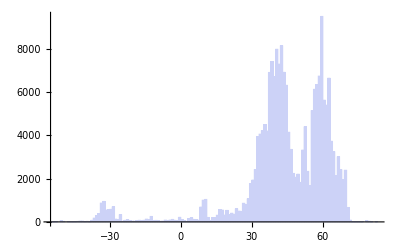

```mathematica
Histogram[d[[All,5]]](*The distribution of latitudes in the data*)
```

```mathematica
Show[ListPlot[d[[All,{4,5}]],PlotStyle->{RGBColor[0,0,0]},PlotRange->{{-180,180},{-90,90}}],ListPlot[d[[mamer,{4,5}]],PlotStyle->{PointSize[.02],RGBColor[1,0,0]}]]
```

-Graphics-

```mathematica
nn=Dimensions[nubes[[#]]][[1]]&/@Range[1,135];
```

(*the number of elements in each time-slot*)

(*
d contains the GBIF points for the 190 species. nubes is an Array of nn[[t]]X7 with the IDs, coordinates and variables of the t=1,2...135 time-slices
*)

```mathematica
tally=Tally[d[[All,3]]];
```

```mathematica
size=Table[tally[[j,2]],{j,1,190}];
```

(*
Tally and size contain the index of the species and how many points it contains, and size is how many points
*)

```mathematica
Dimensions[tally]
```

{190,2}

```mathematica
ind2=Accumulate[tally[[All,2]]];
```

```mathematica
ind=Join[{0},ind2];
```

(*
ind is the index of where in d is it that a specie begins.
*)

```mathematica
vars2=Table[d[[Range[ind[[i]]+1,ind[[i+1]]],{6,7,8}]],{i,1,190}];
```

```mathematica
crds2=Table[d[[Range[ind[[i]]+1,ind[[i+1]]],{4,5}]],{i,1,190}];
```

(*
vars2 and crds2 contain the bio10, bio11 and bio12 data for the OBSERVATIONS, and the Latitude and Longitude, for all i = 1,2...190 species.
I need to spot species with very few points (<9) OR highly correlated (> 0.975) axes
*)

```mathematica
nonfaulty=Table[If[size[[j]]<9,0,If[ (Abs[Correlation[1.*vars2[[j]]][[1,2]]]>.975∨Abs[Correlation[1.*vars2[[j]]][[1,3]]]>.975),0,1]],{j,1,190}];
```

```mathematica
enough=Flatten[Position[nonfaulty,1]];
```

```mathematica
Dimensions[size]
```

{190}

```mathematica
Dimensions[enough]
```

{183}

(*
since in enough I have the indices of the species with enough and well-behaved data, I can simply use enough as the set of indices of the nice species
*)

```mathematica
Dimensions[vars2]
```

{190}

```mathematica
vars=vars2[[enough]];
```

```mathematica
crds=crds2[[enough]];
```

```mathematica
names=names2[[enough]];
```

```mathematica
Position[names,"Mazama_americana"]
```

{{86}}

```mathematica
vars[[1]]
```

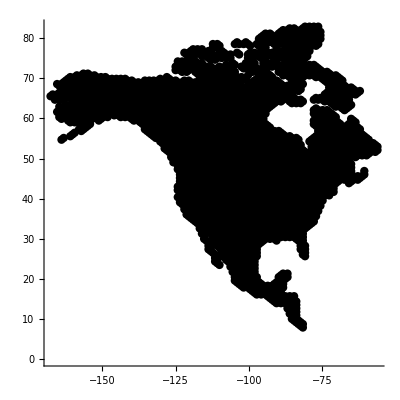

```mathematica
fondo=ListPlot[nubes[[1,;;,{3,4}]],PlotStyle->{RGBColor[0,0,0],PointSize[.015]},AspectRatio->1]
```

```mathematica
areas=Table[Show[fondo,ListPlot[crds[[j]],PlotStyle->Directive[{PointSize[.02],Hue[j/50]}]],PlotLabel->names[[j]]],{j,1,183,1}];
```

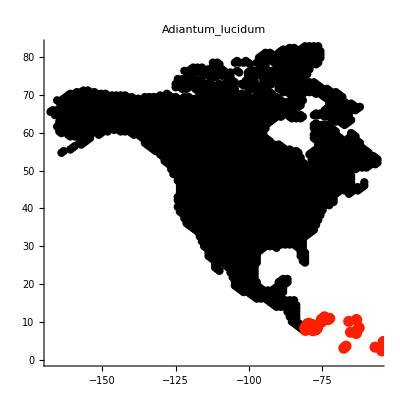
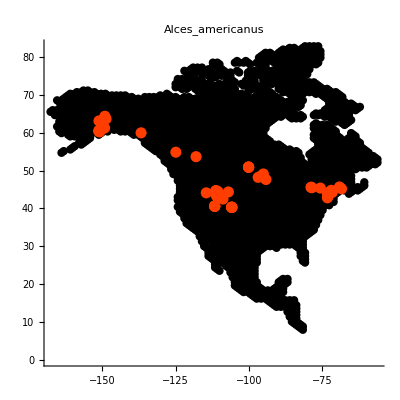
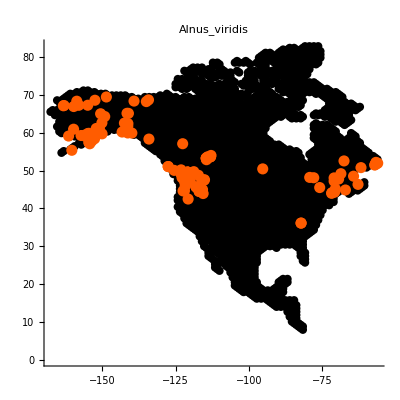
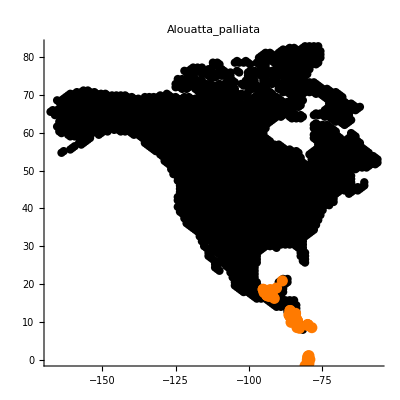
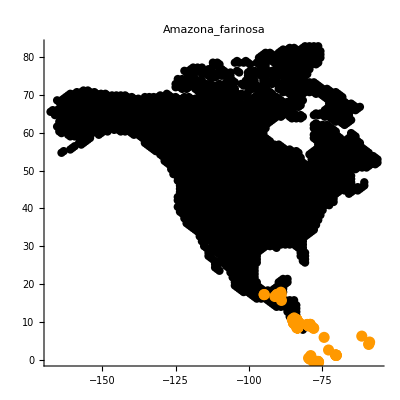
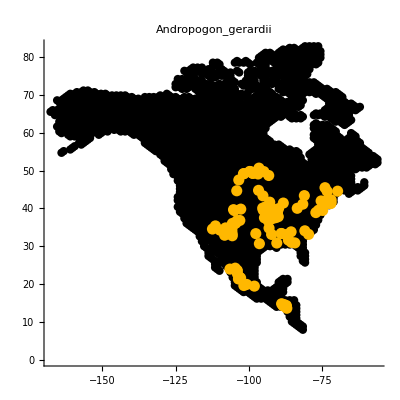
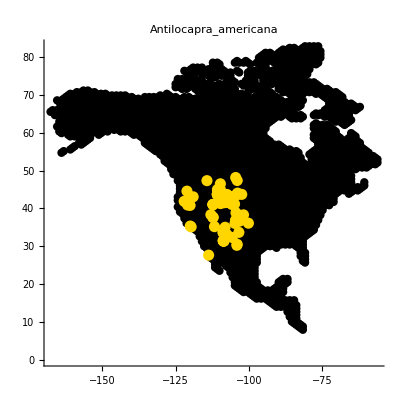
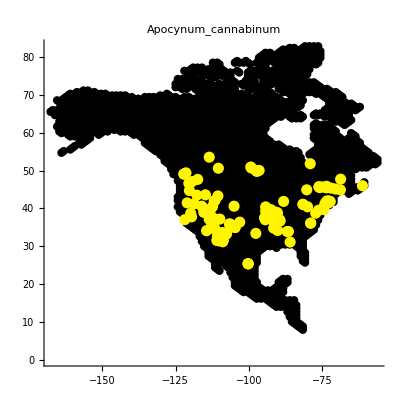

```mathematica
areas[[1;;10]]
```

```mathematica
puntos=Table[ListPointPlot3D[vars[[j]],PlotStyle->Directive[{PointSize[.02],Hue[j/20]}],Axes->False,Boxed->False],{j,1,183}];
```

```mathematica
puntos[[1;;10]]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Needs["MultivariateStatistics`"](*To fit niches I need ellipsoids*)
```

```mathematica
v={v1,v2,v3}
```

{v1,v2,v3}

```mathematica
Array[frmq,183];
```

```mathematica
Monitor[
Do[
(*
mnvlellipse[Transpose[tt[[enough[[i]]]]],.001];
frmsquad[i]=(cent-v).Inverse[A].Transpose[{cent-v}]
*)
el=EllipsoidQuantile[vars[[i]],.9];
(*
Notice the elements of the object el: [[1]] is the centroid, [[2]] is the vector of stretches (λ=1/stretch^2, and [[3]] is the matrix U of eigenvectors. Therefore the matrix sigma needs to be calculated from these elements...
*)
mu=el[[1]];
sigma=Transpose[el[[3]]].DiagonalMatrix[1/el[[2]]^2].el[[3]];
frmq[i]=FullSimplify[(v-mu).sigma.Transpose[{v-mu}]];
,
{i,1,183}
],i
]
```

```mathematica
(*
As a precaution
*)
```

```mathematica
fmqq=frmq
```

frmq

```mathematica
fmqq[1]
```

{98.8899+0.0121108 v1^2+0.0115079 v2^2+v1 (-0.793281-0.0222832 v2-0.0000203515 v3)+v2 (0.0835144+0.0000244884 v3)+(-0.00324099+5.24191×10^-7 v3) v3}

```mathematica
eggs=Monitor[Table[ContourPlot3D[fmqq[j]==1,{v1,-200,500},{v2,-300,500},{v3,-1000,5500},Mesh->None,PlotLabel->names[[j]],ContourStyle->Directive[{White,Opacity[.2]}],AxesLabel->{Style["Tmax",Bold,Blue],Style["Tmin",Bold,Blue],Style["Precip",Bold,Blue]}],{j,1,183}],j];
```

```mathematica
Table[Show[eggs[[j]],puntos[[j]],ImageSize->250],{j,1,87}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
(*
Now I am going to do some cute manipulations
*)
```

```mathematica
Manipulate[ListPointPlot3D[nubes[[t]][[Range[1,nn[[t]]],{5,6,7}]],AxesLabel->{Style["Tmax",Bold,Blue],Style["Tmin",Bold,Blue],Style["Precip",Bold,Blue]},PlotRange->{{-200,400},{-600,600},{0,4000}},ImageSize->700],{t,1,135,1}]
```

```mathematica
(*
Now I am going to create a largish Array, that contains the indices in each slice of nubes, of the cells with suitable climate for each species. So this is an Array of dimensions 183X135XNumber_of_suitable_cells. 
*)
Array[suitable,183];
```

```mathematica
Monitor[
suitable=
Table[(*Runs on the j =1, 2...183 species*)
Table[(*Runs on the 135 layers. Index t*)
Flatten[Position[
Table[(*runs on the number of rows of the t climatic layer. Index i*)
If[(*Checks if a point is inside an egg*)(fmqq[j]/.{v1->nubes[[t]][[i,5]],v2->nubes[[t]][[i,6]],v3->nubes[[t]][[i,7]]})[[1]]<1,1,0],
{i,1,nn[[t]]}],1]],
{t,1,135}],
{j,1,183}],
{j,t,i}]
```

{{{4599,4605,4609,4612,4614,4617,4619,4622,4623,4624,4626,4627,4629,4630,4631,4632,4634,4635,4636},{4599,4605,4609,4612,4614,4617,4619,4622,4623,4624,4626,4627,4629,4630,4631,4632,4634,4635,4636},{4599,4605,4609,4612,4614,4617,4619,4622,4623,4624,4626,4627,4629,4630,4631,4632,4634,4635,4636},{4599,4605,4609,4612,4614,4617,4619,4622,4623,4624,4626,4627,4629,4630,4631,4632,4635,4636},«127»,{},{},{},{}},«181»,{{286,311,329,«1528»,3836,3867},«134»}}

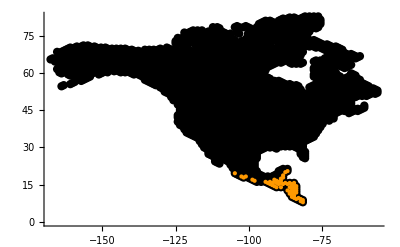

```mathematica
Show[fondo,ListPlot[nubes[[1,suitable[[5,1]],{3,4}]],Axes->False,PlotStyle->{Hue[5/50]}]]
```

```mathematica
Dimensions[suitable]
```

{183,135}

```mathematica
Dimensions[nubes]
```

{135}

```mathematica
Dimensions[nubes[[1]]]
```

{4636,7}

```mathematica
Manipulate[If[Dimensions[suitable[[j,t]]][[1]]>1,Show[fondo,ListPlot[nubes[[t,suitable[[j,t]],{3,4}]],Axes->False,PlotStyle->{Hue[j/50]}]],Show[fondo]],{j,1,183,1},{t,1,135,1}]
```

```mathematica
ListPlot[nubes[[90,suitable[[1,90]],{3,4}]],Axes->False,PlotStyle->{Hue[1/50]}]
```

```mathematica
suitable[[1,30]]
```

{4525,4545,4548,4549,4551,4553}

```mathematica
ListPointPlot3D[nubes[[1,All,{5,6,7}]],PlotStyle->Directive[{PointSize[.002],RGBColor[0,0,0]}],Boxed->False,Axes->False]
```

-Graphics3D-

```mathematica
Manipulate[If[Dimensions[suitable[[j,t]]][[1]]>1,Show[eggs[[j]],ListPointPlot3D[nubes[[t,suitable[[j,t]],{5,6,7}]],Axes->False,PlotStyle->{Hue[j/50]}],ListPointPlot3D[nubes[[t,All,{5,6,7}]],PlotStyle->Directive[{PointSize[.002],RGBColor[0,0,0]}],Boxed->False,Axes->False]],Show[eggs[[j]]]],{j,1,183,1},{t,1,135,1}]
```

```mathematica
mg=Manipulate[GraphicsGrid[{{If[Dimensions[suitable[[20,t]]][[1]]>1,Show[fondo,ListPlot[nubes[[t,suitable[[20,t]],{3,4}]],Axes->False,PlotStyle->{Hue[20/50]}]],Show[fondo]],If[Dimensions[suitable[[20,t]]][[1]]>1,Show[eggs[[20]],ListPointPlot3D[nubes[[t,suitable[[20,t]],{5,6,7}]],Axes->False,PlotStyle->{Hue[20/50]}],ListPointPlot3D[nubes[[t,All,{5,6,7}]],PlotStyle->Directive[{PointSize[.002],RGBColor[0,0,0]}],Boxed->False,Axes->False]],Show[eggs[[20]]]]}},ImageSize->900],{t,1,135,1}]
```

```mathematica
Export["Z:\\Andres_Backup\\PanoramaSpecies\\Buteloua_aristidoides.gif",mg]
```

Z:\Andres_Backup\PanoramaSpecies\Buteloua_aristidoides.gif

```mathematica
(*


*)
```

```mathematica
Clear[cubos]
```

```mathematica
Array[cubos,135];
```

```mathematica
Monitor[
Do[
mat1=ConstantArray[0,{nn[[t]],183}];
unosc=ConstantArray[1,183];
Do[mat1[[suitable[[j,t]],j]]=1,{j,1,183}];
alfas=Flatten[mat1.unosc];
(* The following two lines separate cells with no species. 
ind=Flatten[Position[If[alfas[[#]]>0,1,0]&/@Range[1,nn[[t]]],1]];
cubos[t]=Join[nubes[[t,ind]],Partition[alfas[[ind]],1],2],
*)
cubos[t]=Join[nubes[[t,All]],Partition[alfas[[All]],1],2],(*this line does not separate zeroes*)
{t,1,135}],
t]
```

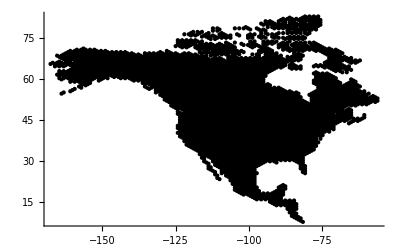

```mathematica
Graphics[{Thick,Point[cubos[60][[All,{3,4}]],VertexColors->(Hue[#/100]&/@cubos[60][[All,8]])]},AspectRatio->1/GoldenRatio,Axes->True]
```

```mathematica
Manipulate[Graphics3D[{Thick,Point[cubos[t][[All,{5,6,7}]],VertexColors->(Hue[#/100]&/@cubos[t][[All,8]])]},PlotRange->{{-100,300},{-500,400},{0,4000}},BoxRatios->{1,1,.5},Axes->True],{t,1,135,1}]
```

```mathematica
Manipulate[Graphics[{Thick,Point[cubos[t][[All,{3,4}]],VertexColors->(Hue[#/100]&/@cubos[t][[All,8]])]},AspectRatio->1/GoldenRatio,Axes->True],{t,1,135,1}]
```

```mathematica
ListPointPlot3D[cubos[1][[;;,{5,6,7}]],PlotStyle->{Hue[98/100]}]
```

-Graphics3D-

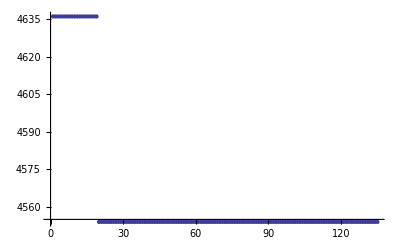

```mathematica
ListPlot[Join[Partition[Range[1,135],1],Partition[Dimensions[cubos[#]][[1]]&/@Range[1,135],1],2]]
```

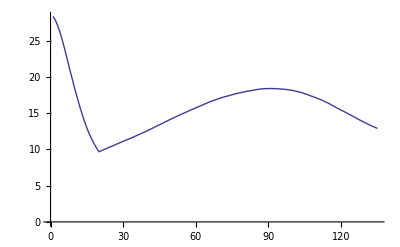

```mathematica
ListLinePlot[Mean[cubos[#][[All,8]]]&/@Range[1,135]]
```

```mathematica
//N
```

```mathematica
f[g_]:=cubos[1][[All,8]]/183
```

```mathematica
f[1];
```

```mathematica
ListPointPlot3D[cubos[1][[All,{5,6,7}]],ColorFunctionScaling->False,ColorFunction->(Hue[f[##]/183]&)]
```

```mathematica
Timing[Graphics3D[{Hue[Last[#]/100],Point[Take[#,{5,7}]]}&/@cubos[1],PlotRange->{{0,300},{-400,400},{0,4000}},BoxRatios->{1,1,.5},Axes->True]]
```

{0.016,-Graphics3D-}

```mathematica
Timing[Graphics3D[{Thick,Point[cubos[1][[All,{5,6,7}]],VertexColors->(Blend[{{0,Blue},{10,Green},{50,Yellow},{100,Red}},#]&/@cubos[1][[All,8]])]},PlotRange->{{-100,300},{-500,400},{0,4000}},BoxRatios->{1,1,.5},Axes->True]]
```

{0.,-Graphics3D-}

```mathematica
es=Monitor[Table[Graphics3D[{Hue[Last[#]/100],Point[Take[#,{5,7}]]}&/@cubos[t],PlotRange->{{0,300},{-400,400},{0,4000}},BoxRatios->{1,1,.5},Axes->True],{t,1,135,1}],t](*far too slow also*)
```

```mathematica
Manipulate[es[[t]],{t,1,135,1}]
```

```mathematica
es2=Table[ListPointPlot3D[List/@cubos[t][[All,{5,6,7}]],PlotStyle->({PointSize[.01],Blend[{{0,Darker[Blue]},{50,Yellow},{100,Red}},#1]}&/@Flatten[cubos[t][[All,8]]])],{t,1,20}]
```

{-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-,-Graphics3D-}

```mathematica
Manipulate[es2[[t]],{t,1,20}]
```

```mathematica
es2[[1]]
```

-Graphics3D-

```mathematica
Graphics3D[Point[cubos[1][[All,5;;7]],VertexColors->(Blend[{{0,Darker[Blue]},{50,Yellow},{100,Red}},#])&/@cubos[1][[All,8]]],Axes->True,BoxRatios->{1,1,1/GoldenRatio}]
```

-Graphics3D-

```mathematica
Blend[{{0,Darker[Blue]},{50,Yellow},{100,Red}},#]&/@cubos[1][[All,8]]
```

{RGBColor[1/25,1/25,16/25],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[1/50,1/50,49/75],RGBColor[1/25,1/25,16/25],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],RGBColor[0,0,2/3],«4616»,RGBColor[31/50,31/50,19/75],RGBColor[17/50,17/50,11/25],RGBColor[27/50,27/50,23/75],RGBColor[3/5,3/5,4/15],RGBColor[3/5,3/5,4/15],RGBColor[14/25,14/25,22/75],RGBColor[17/50,17/50,11/25],RGBColor[11/25,11/25,28/75],RGBColor[27/50,27/50,23/75],RGBColor[27/50,27/50,23/75]}

```mathematica
Manipulate[Graphics3D[{Thick,Point[cubos[t][[All,{5,6,7}]],VertexColors->(Blend[{{0,Blue},{10,Green},{50,Yellow},{100,Red}},#]&/@cubos[t][[All,8]])]},PlotRange->{{-100,300},{-500,400},{0,4000}},BoxRatios->{1,1,.5},Axes->True],{t,1,135,1}]
```

```mathematica
Max[cubos[#][[All,8]]]&/@Range[1,135]
```

{92,93,92,92,94,91,89,91,91,93,93,92,93,92,91,91,86,88,89,88,88,89,89,88,88,88,89,88,89,89,89,90,91,91,92,92,91,91,93,93,93,93,93,93,92,92,94,94,93,92,92,92,91,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,92,91,91,91,91,91,91,91,92,92,91,90,90,90,90,90,90,90,89,90,91,90,90,90,91,91,91,90,90,91,92,91,91,91,91,92,92,91,91,92,92,92,92,92,92,92,92,91,91,91,91,90,91,91,91,91,90,91,90,90,90,91,91,91,91,91}

```mathematica
ind
```

```mathematica
mat1.unosc
```

```mathematica
Flatten[Position[If[alfas[[#]]>0,1,0]&/@Range[1,nn[[t]]],1]]
```

```mathematica
nn[[135]]
```

4554

```mathematica
Dimensions[ind]
```

{10188}

```mathematica
Dimensions[nubes[[135,ind]]]
```

{10188,7}

```mathematica
Dimensions[cubos]
```

{}

```mathematica
cubos[1]
```

{{4,594,-80.75,82.8349,9.4,-379.6,70,2},{5,595,-79.25,82.8349,-8.55,-393.6,112.1},{5,595,-79.25,82.8349,-8.55,-393.6,112.1},«9759»,{5212,19105,-81.5,7.92374,263.45,246.4,3283.75},{5,595,-79.25,82.8349,-8.55,-393.6,112.1}}

```mathematica
Dimensions[mat1]
```

{4636,183}

```mathematica
Transpose[{unosc}]
```

{{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},«4526»,{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1},{1}}

```mathematica
mat1
```

```mathematica
ConstantArray[0,{25,5}]
```

{{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0},{0,0,0,0,0}}

```mathematica
nn
```

{4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4636,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554,4554}

```mathematica
suitable[[1,1]]
```

{4599,4605,4609,4612,4614,4617,4619,4622,4623,4624,4626,4627,4629,4630,4631,4632,4634,4635,4636}

```mathematica
aux1=Join[nubes[[1,ind1]],Partition[alfas[[ind1]],1],2]
```

Part::partw: Part 4555 of {{6}, {1}, {2}, {1}, {2}, {0}, {3}, {0}, {0}, {1}, {1}, {1}, {0}, {0}, {1}, {2}, {0}, {0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {3}, {3}, {2}, {1}, {0}, {0}, {0}, {3}, {0}, {1}, {1}, {1}, {1}, {0}, {0}, {0}, {0}, {0}, {0}, {3}, {3}, {1}, « 4504 »} does not exist.

Join::heads: Heads List and Part at positions 1 and 2 are expected to be the same.

Join::headsd: Expression {{6}, {1}, {2}, {1}, {2}, {0}, {3}, {0}, {0}, {1}, {1}, {1}, {0}, {0}, {1}, {2}, {0}, {0}, {1}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {0}, {3}, {3}, {2}, {1}, {0}, {0}, {0}, {3}, {0}, {1}, {1}, {1}, {1}, {0}, {0}, {0}, {0}, {0}, {0}, {3}, {3}, {1}, « 4504 »} ⟦ {1, 5, 6, 11, 12, 13, 33, 34, 35, 39, 45, 46, 56, 57, 58, 59, 60, 71, 72, 73, 75, 80, 81, 84, 85, 86, 87, 88, 89, 95, 99, 100, 101, 102, 103, 114, 116, 117, 118, 120, 121, 125, 126, 128, 129, 130, 131, 132, 137, 138, « 4461 »} ⟧ at position 2 is expected to have head List for all subexpressions through level 2.

Join[{{4,594,-80.75,82.8349,9.4,-379.6,70},{11,698,-86,82.4019,13.6,-391.45,66.3},{12,699,-84.5,82.4019,13.55,-388.45,65.4},«4506»,{5210,18997,-82.25,8.35675,274.4,257.35,2912.25},{5212,19105,-81.5,7.92374,263.45,246.4,3283.75}},{{6},{1},{2},«4548»,{13},{25},{25}}⟦{«1»}⟧,2]

```mathematica
Dimensions[cubo2]
```

{4636,183}

```mathematica
Do[cubo2[[suitable[[j,1]],j]]=1,{j,1,183}]
```

```mathematica
cubo2[[All,1]]
```

```mathematica
unosc=ConstantArray[1,183];
```

```mathematica
alfas=cubo2.unosc;
```

```mathematica
alfas
```

```mathematica
alfas[[1;;20]]
```

{2,0,0,0,1,2,0,0,0,0,1,1,1,0,0,0,0,0,0,0}

```mathematica
ind1=Flatten[Position[If[alfas[[#]]>0,1,0]&/@Range[1,nn[[1]]],1]];
```

```mathematica
nubes1=nubes[[1,ind1]]
```

{{4,594,-80.75,82.8349,9.4,-379.6,70},{11,698,-86,82.4019,13.6,-391.45,66.3},{12,699,-84.5,82.4019,13.55,-388.45,65.4},«4506»,{5210,18997,-82.25,8.35675,274.4,257.35,2912.25},{5212,19105,-81.5,7.92374,263.45,246.4,3283.75}}

```mathematica
Dimensions[alfas]
```

{4636}

```mathematica
Dimensions[ind1]
```

{4511}

```mathematica
Dimensions[nubes[[1]]]
```

{4636,7}

```mathematica
Dimensions[nubes[[1]]]
```

{4636,7}

```mathematica
nubes[[1,suitable[[1,1]],{3,4}]]
```

{{-91.25,14.4189},{-90.5,13.9859},{-84.5,13.9859},{-83.75,13.5529},{-84.5,13.1199},{-83.75,12.6869},{-84.5,12.2539},{-86,11.3878},{-84.5,11.3878},{-85.25,10.9548},{-84.5,10.5218},{-85.25,10.0888},{-84.5,9.65579},{-83,9.65579},{-83.75,9.22278},{-82.25,9.22278},{-81.5,8.78976},{-82.25,8.35675},{-81.5,7.92374}}

```mathematica
aux1=Join[nubes[[1,ind1]],Partition[alfas[[ind1]],1],2]
```

{{4,594,-80.75,82.8349,9.4,-379.6,70,2},{11,698,-86,82.4019,13.6,-391.45,66.3,1},{12,699,-84.5,82.4019,13.55,-388.45,65.4,2},«4506»,{5210,18997,-82.25,8.35675,274.4,257.35,2912.25,27},{5212,19105,-81.5,7.92374,263.45,246.4,3283.75,27}}

```mathematica
Dimensions[aux1]
```

{4511,8}

ListPlot::icolscale: -- Message text not found -- ({Hue[1/183]})

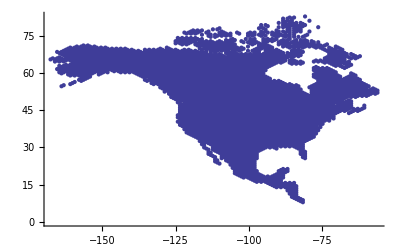

```mathematica
ListPlot[aux1[[All,{3,4}]],ColorFunction->(ps)]
```

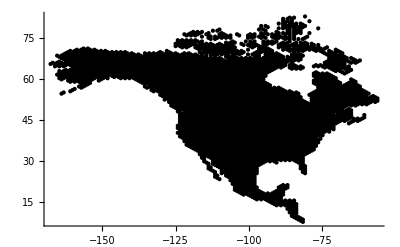

```mathematica
Graphics[{Thick,Point[aux1[[All,{3,4}]],VertexColors->(Hue[#/183]&/@aux1[[All,8]])]},AspectRatio->1/GoldenRatio,Axes->True]
```

```mathematica
ps={PointSize[.1],Hue[(#-min)/(max-min)]}&/@cubos[1][[;;,8]];
```

```mathematica
min=Min[cubos[1][[;;,8]]]
```

1

```mathematica
max=Max[cubos[1][[;;,8]]]
```

92

```mathematica
ListPointPlot3D[nubes[[1,All,{5,6,7}]]]
```

-Graphics3D-

```mathematica
t1=Table[RandomVariate[NormalDistribution[3],4],{500}];
```

```mathematica
Dimensions[t1]
```

{500,4}

```mathematica
Dimensions[nubes[[1,All, {5,6,7}]]]
```

{4636,3}

```mathematica
Dimensions[suitable[[1,1]]]
```

{19}

```mathematica
Dimensions[cubos[suitable[[1,1]]]]
```

{1}

```mathematica
Dimensions[ind]
```

{3826}

```mathematica
Dimensions[cubos[1][[All,{5,6,7}]]]
```

{4511,3}

```mathematica
F[x_,y_,z_]:=cubos[1][[All,8]]/100
```

```mathematica
F[1,1,1]
```

```mathematica
ListPointPlot3D[cubos[1][[All,{5,6,7}]],ColorFunctionScaling->False,ColorFunction->(Hue[F[##]][[1]]&)](* astonishing slow!!*)
```

$Aborted[]

```mathematica
Export["Z:\\Andres_Backup\\PanoramaSpecies\\Amazona_farinosa.gif",%]
```

```mathematica
Export["Z:\\Andres_Backup\\PanoramaSpecies\\Amazona_farinosa2.swf",%]
```